## First part

```mathematica
WebImageSearch["Resistor", "Thumbnails"]
```

$Aborted

```mathematica
ColorQuantize[-Graphics-,14]
```

-Graphics-

```mathematica
ColorQuantize[ColorConvert[-Graphics-,"CMYK"],14]
```

-Graphics-

```mathematica
Map[ColorQuantize[#,14]&,WebImageSearch["Resistor", "Thumbnails"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pictures = WebImageSearch["resistor","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
img = -Graphics-;
saturated = Binarize[ColorConvert[img, "Grayscale"], .9]
Inpaint[img, Dilation[saturated, DiskMatrix[20]]]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[a]
```

```mathematica
ColorQuantize[-Graphics-, 10]
```

-Graphics-

```mathematica
MorphologicalComponents[-Graphics-]//Colorize
```

-Graphics-

```mathematica
lenet=NetChain[
{
ConvolutionLayer[20,5],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
500,
Ramp,
10,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

```mathematica
ImageIdentify[-Graphics-]
```

resistor

```mathematica
Entity["Concept","Resistor::d7w57"]["Properties"]
```

{alternate names,broader concepts,definition,equivalent entity,name,narrower concepts,similar entities,subset concepts,superset concepts,WordData senses,WordNet ID}

```mathematica
ImageAlign[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
WebImageSearch["Resistor","Images","MaxItems"->1]
```

{-Graphics-}

```mathematica
DeleteSmallComponents @ChanVeseBinarize[-Graphics-]
```

-Graphics-

```mathematica
HistogramTransform @ ImageAdjust[-Graphics-]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

-Graphics-

```mathematica
ColorQuantize[ImageAdjust[-Graphics-,1],14]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
CrossingDetect[-Graphics-]
```

-Graphics-

```mathematica
ContourDetect[-Graphics-]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
GradientFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
LaplacianGaussianFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = EdgeDetect[-Graphics-]
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

-Graphics-

```mathematica
Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]
```

Massachusetts, United States

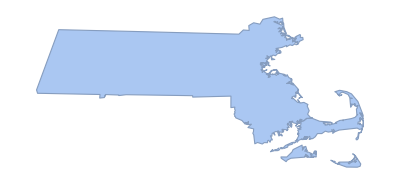

```mathematica
BoundaryDiscretizeGraphics[Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]]
```

## From article

```mathematica
img = RemoveAlphaChannel[-Graphics-];
img = RemoveAlphaChannel[-Graphics-];
img = ImageResize[img, {500}];
img = ColorConvert[RemoveAlphaChannel[img],"RGB"];
```

```mathematica
meanColorMask[image_,mask_ ]:= Module[
{toRemove,imgList},
toRemove = PixelValuePositions[mask, Black];
imgList = Transpose @ ImageData[image];
imgList = Delete[imgList, toRemove];
RGBColor[Mean[Catenate @ imgList]]
]
```

```mathematica
(*getBackColor[image_] := Module[
{edge},
	edge = ImageCrop[image,{10,10},{Right,Bottom}];
	RGBColor [Mean @ Catenate[ImageData[edge]]]
]*)
getBackColor[image_] := meanColorMask[image, AlphaChannel[RemoveBackground[image]] - 1];
backColor = getBackColor[img]
```

RGBColor[{0.97908783178413, 0.9788836902105641, 0.9786489688680372}]

```mathematica
absoluteSubstract[image_, color_] := ImageApply[
	MapThread[
		Abs[#1 - #2]&,
		{Flatten[#],Flatten[List @@ color]}
	]&,
	image
]
substracted = absoluteSubstract[img, backColor]
```

-Graphics-

```mathematica
monochromatic = ColorConvert[substracted,"Grayscale"]
```

-Graphics-

```mathematica
threshold[n_] := Module[
	{num, p, ω, μ, μT, maxK, maxσ, σ2B, temp, k},
	num = Total[n];
	p = n / num;
	ω := Sum[p[i],{i,0,#}]&;
	μ := Sum[(i+1) * p[i], {i, 0, #}]&;
	μT = μ[255];
	σ2B[x_Integer] := Module[
		{μk, ωk},
		ωk = ω[x];
		μk = μ[x];
		If[ ωk ≠ 0 && ωk ≠ 1,
			((μT*ωk - μk)^2) / (ωk * (1 - ωk)),
			-1
		]
	];
	maxσ = 0;
	maxK = 255;
	For[k = 0, k < 255, k++,
		temp = σ2B[k];
		If[ NumberQ[temp] && temp > maxσ,
			maxσ = temp;
			maxK = k;
		]
	];
	maxK
]
```

-Graphics-

305

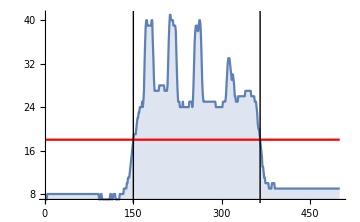
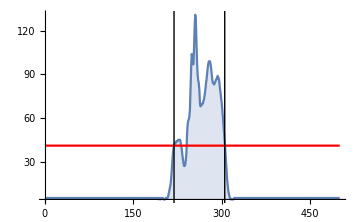
-Graphics- | -Graphics-
Horizontal mean | Vertical mean

-Graphics-

```mathematica
matr = ImageData[monochromatic];
verMean = Map[
	Mean[Flatten[#]]&,
	matr
];
verMean = Round[verMean * 255];
horMean = Map[
	Mean[Flatten[#]]&,
	Transpose[matr]
];
horMean = Round[horMean * 255];

horFrequency = Counts[Catenate[{horMean,Range[0,255]}]] - 1;
verFrequency = Counts[Catenate[{verMean,Range[0,255]}]] - 1;
verThreshold = threshold[verFrequency];
horThreshold = threshold[horFrequency];

verPlot = DiscretePlot[
	verMean[[x]],
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium
];
verThresholdPlot = Plot[
	verThreshold,
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

horPlot = DiscretePlot[
	horMean[[x]],
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium
];
horThresholdPlot = Plot[
	horThreshold,
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

xPos = Values @ Cases[
	MapIndexed[#1->First[#2]&, horMean],
	(x_->y_)/;x>= horThreshold
];
xStart = Min[xPos];
xEnd = Max[xPos];

yPos = Values @ Cases[
	MapIndexed[#1->First[#2]&, verMean],
	(x_->y_)/;x>= verThreshold
];
yStart = Min[yPos];
yEnd = Max[yPos];

segmented = ImageTake[
	img,
	{yStart, yEnd},{xStart, xEnd}
]
xStartLine = Graphics @ Line[{{xStart, 0},{xStart, 255}}];
xEndLine = Graphics @ Line[{{xEnd, 0},{xEnd, 255}}];
yStartLine = Graphics @ Line[{{yStart, 0},{yStart, 255}}];
yEndLine = Graphics @ Line[{{yEnd, 0},{yEnd, 255}}];
yEnd
Grid[{
	{
		Show[{horPlot, horThresholdPlot, xStartLine, xEndLine}],
		Show[{verPlot, verThresholdPlot, yStartLine, yEndLine}]
	},
	{"Horizontal mean", "Vertical mean"}
}]

extracted = ImageCrop[segmented, {ImageDimensions[segmented][[1]], 15}, Center]
```

```mathematica
RemoveBackground[extracted]
```

-Graphics-

```mathematica
mainColor = getBackColor[extracted]
```

RGBColor[{0.5788359270496836, 0.4648200711232944, 0.27526834361032065}]

```mathematica
ClusteringComponents[extracted,12,
 DistanceFunction->EuclideanDistance,
Method->"KMeans"
] // Colorize
```

-Graphics-

```mathematica
extractedSub = absoluteSubstract[extracted, mainColor]
```

-Graphics-

```mathematica
extractedMono = ColorConvert[extractedSub, "Grayscale"]
```

-Graphics-

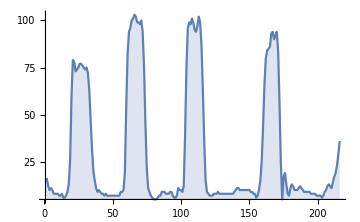

```mathematica
extractedMeans = Map[
	Mean[Flatten[#]]&,
	Transpose[ImageData[extractedMono]]
];
extractedMeans = Round[extractedMeans * 255];
extractedPlot = DiscretePlot[
	extractedMeans[[x]],
	{x, 1, Length[extractedMeans]},
	PlotRange->All,
	ImageSize->Medium
];
Show[{extractedPlot}]
```

## Dividing the image in sections

```mathematica
(*mask = Binarize[substracted]*)
mask =AlphaChannel[RemoveBackground[img]]
```

-Graphics-

```mathematica
PixelValuePositions[mask, Black]
```

{{1,500},{2,500},{3,500},{4,500},{5,500},{6,500},{7,500},{8,500},{9,500},{10,500},{11,500},{12,500},{13,500},{14,500},{15,500},222212,{487,1},{488,1},{489,1},{490,1},{491,1},{492,1},{493,1},{494,1},{495,1},{496,1},{497,1},{498,1},{499,1},{500,1}}
 |  |  |  |

```mathematica
meanColorMask[image_,mask_ ]:= Module[
{toRemove,imgList},
toRemove = PixelValuePositions[mask, Black];
imgList = Transpose @ ImageData[image];
imgList = Delete[imgList, toRemove];
RGBColor[Mean[Catenate @ imgList]]
]
```

```mathematica
maskColumns =First @ ImagePartition[mask, {10, ImageData[img][[1]]//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
columns =First @ ImagePartition[img,{10, ImageData[img][[1]]//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[meanColorMask[columns[[x]],maskColumns[[x]]],{x,Length[columns]}]
```

{RGBColor[{0.8289014235831317, 0.8318560300832654, 0.857301459396543}],RGBColor[{0.8171347818406639, 0.8209680268503795, 0.8438085143967495}],RGBColor[{0.8116078431372549, 0.8151808278867095, 0.8382396514161221}],RGBColor[{0.823876892529164, 0.8211632332257801, 0.8457847273930674}],RGBColor[{0.8227180527383371, 0.8181879648411087, 0.8431372549019605}],RGBColor[{0.8189542483660129, 0.8146263910969795, 0.8373608903020666}],RGBColor[{0.8414469235970249, 0.8386916835699801, 0.8537525354969582}],RGBColor[{0.8578594771241828, 0.855833333333333, 0.8658823529411772}],RGBColor[{0.8563295493636053, 0.8543171654626769, 0.8642586859305127}],RGBColor[{0.8538852578068268, 0.8526870007262167, 0.8605482933914302}],RGBColor[{0.8472014260249555, 0.8472014260249555, 0.8507664884135474}],RGBColor[{0.8454764361885108, 0.8454764361885108, 0.849518403852769}],RGBColor[{0.8685180509972232, 0.8678279895649251, 0.8718505427922234}],RGBColor[{0.8533558226157858, 0.8459624710099096, 0.8082507554993321}],RGBColor[{0.7690441176470593, 0.7298120915032683, 0.6540849673202611}],RGBColor[{0.7104342595934082, 0.6492289185612895, 0.5157560447491886}],RGBColor[{0.7361079138143423, 0.5781506835483948, 0.42976515013832495}],RGBColor[{0.6679879810470354, 0.27948688316191017, 0.2729958781154906}],RGBColor[{0.7296762693347144, 0.5086577348436934, 0.40119218752994945}],RGBColor[{0.7090620031796498, 0.6356866670592175, 0.45306875502954036}],RGBColor[{0.6968942321454152, 0.5930646711239251, 0.4775889918011003}],RGBColor[{0.4724230591594247, 0.32332787504723653, 0.40563882940756724}],RGBColor[{0.683626287624003, 0.5745203798887412, 0.5242380015652444}],RGBColor[{0.7695907928388769, 0.6984612105711865, 0.5470119352088673}],RGBColor[{0.7769465681009247, 0.689467365893725, 0.5594785282534076}],RGBColor[{0.583696943176847, 0.44521681148548936, 0.3951490904544606}],RGBColor[{0.6310171829926002, 0.5004473431163512, 0.42373426982733536}],RGBColor[{0.7682763288702763, 0.6864310341180702, 0.5133151426697974}],RGBColor[{0.7713768115942049, 0.6928388746803065, 0.5264578005115096}],RGBColor[{0.785316423427444, 0.7120175047267016, 0.5520404478150959}],RGBColor[{0.7414127596070139, 0.6592505078141202, 0.4929113294366388}],RGBColor[{0.65546388080964, 0.5847450584673828, 0.42762905363961995}],RGBColor[{0.7767272870880501, 0.7013920976245489, 0.5511245384357171}],RGBColor[{0.7809360528130874, 0.6958202778598874, 0.5364035865602529}],RGBColor[{0.7615203619909504, 0.6810216189039718, 0.5206073403720474}],RGBColor[{0.7392468805704101, 0.6833912655971495, 0.5794786096256698}],RGBColor[{0.8294010889292204, 0.8170029536315445, 0.7618803601295348}],RGBColor[{0.9087145969498927, 0.8944081336238207, 0.8586661825223918}],RGBColor[{0.8979965899403242, 0.9009519749928963, 0.9116084114805337}],RGBColor[{0.9050359712230212, 0.9029623360135414, 0.9162787417125116}],RGBColor[{0.9201579912540561, 0.9177740160812526, 0.9308082945408377}],RGBColor[{0.9101234567901237, 0.9081190994916489, 0.9192592592592597}],RGBColor[{0.9131735657225852, 0.9116485112563549, 0.9199709513435008}],RGBColor[{0.915831517792302, 0.9142338416848221, 0.9225998547567177}],RGBColor[{0.9229629629629634, 0.9218300653594773, 0.9283224400871458}],RGBColor[{0.924444444444444, 0.924444444444444, 0.924444444444444}],RGBColor[{0.9186492374727665, 0.9186347131445166, 0.918605664488017}],RGBColor[{0.9175887455353889, 0.9175595888913186, 0.917924046942197}],RGBColor[{0.9055203619909495, 0.9040874811463044, 0.9118552036199089}],RGBColor[{0.9006684491978607, 0.8991532976827092, 0.9074420677361852}]}

```mathematica
resistorBackColor = meanColorMask[img, mask]
```

RGBColor[{0.7861002269633819, 0.6781417655109769, 0.5628677010814515}]

```mathematica
Table[RGBColor @ Mean[Catenate[ImageData[columns[[x]]]]],{x,Length[columns]}]
```

{RGBColor[{0.3484621942422474, 0.8470614466522418, 0.8058469407830181}],RGBColor[{0.34401993573349343, 0.8450442651977214, 0.8027096858810547}],RGBColor[{0.3416105974162285, 0.8441917502787116, 0.8015935471178584}],RGBColor[{0.3381152862482843, 0.843113646796512, 0.8004131418453824}],RGBColor[{0.3395160338382898, 0.8436435176077134, 0.8008380877434753}],RGBColor[{0.34067283100531864, 0.8455164273067133, 0.7994583251360906}],RGBColor[{0.3421680110171244, 0.8464633746475217, 0.8002177191947186}],RGBColor[{0.3382425077054327, 0.84402124729491, 0.7975093448750882}],RGBColor[{0.33537805757755407, 0.8436422060463019, 0.7968456947996742}],RGBColor[{0.33587251623057984, 0.8404446193193011, 0.7947734277657685}],RGBColor[{0.3452934618663603, 0.8439241917502862, 0.7922119483244947}],RGBColor[{0.37244278313332924, 0.8541806020066994, 0.7935707259492595}],RGBColor[{0.4164233720244051, 0.8533871073513134, 0.7861341727326587}],RGBColor[{0.521482064397674, 0.8437327037838648, 0.7610217063414172}],RGBColor[{0.5928847793298061, 0.8063322185061401, 0.7069932454587203}],RGBColor[{0.6105410190832327, 0.7862036854875787, 0.6770529215030355}],RGBColor[{0.6244658666142135, 0.7817522460489278, 0.6659177650993375}],RGBColor[{0.657240474785245, 0.6493907797232477, 0.5367932323430944}],RGBColor[{0.6790268214309214, 0.5559302249327824, 0.47406518460226027}],RGBColor[{0.6851688635320433, 0.5543235622008004, 0.47354318315954386}],RGBColor[{0.6702695258705582, 0.668763853367419, 0.5634297330972438}],RGBColor[{0.6384143222506533, 0.7942055216735605, 0.6809758016919096}],RGBColor[{0.6338264804249562, 0.8097737556561155, 0.7000629549478714}],RGBColor[{0.48472949045839686, 0.7380247885107117, 0.71070102957571}],RGBColor[{0.29442586399108545, 0.6630585612170995, 0.7417456882418649}],RGBColor[{0.2875270509541631, 0.663475637746709, 0.7400629549478747}],RGBColor[{0.47549085185914347, 0.7539418978293586, 0.7249183553019911}],RGBColor[{0.5703770739064892, 0.7926211554856093, 0.6918525804970717}],RGBColor[{0.5706997180143, 0.7916178110040036, 0.6886667978227983}],RGBColor[{0.5422388353334672, 0.7712322119483231, 0.6730120007869302}],RGBColor[{0.30991802741164, 0.5932074234375769, 0.5494681618466785}],RGBColor[{0.2636369598006519, 0.5716361728637724, 0.5429313397599836}],RGBColor[{0.28259426847662883, 0.5791671585021767, 0.5439950160666275}],RGBColor[{0.5264397665420721, 0.7609351432880824, 0.6675572168666715}],RGBColor[{0.5622375237720587, 0.789179618335634, 0.686835858089048}],RGBColor[{0.5331746344022661, 0.7622886746671849, 0.651301724703258}],RGBColor[{0.48036854875731105, 0.7084792445406058, 0.5729516689619101}],RGBColor[{0.4814361597481967, 0.6988733687454719, 0.5544219293068432}],RGBColor[{0.5235648239228885, 0.715686274509793, 0.5714682930028251}],RGBColor[{0.5974227818217647, 0.7685920388222236, 0.6491389599317905}],RGBColor[{0.6054272411305771, 0.7707259492425815, 0.6596091546986558}],RGBColor[{0.6044724244212857, 0.76774477014887, 0.6537910682667561}],RGBColor[{0.6031674208144914, 0.7698144140599431, 0.6528100203291901}],RGBColor[{0.601343038887807, 0.7720361990950284, 0.6562515574791663}],RGBColor[{0.6010859728506907, 0.7769637353269121, 0.6606046298117851}],RGBColor[{0.5991920781690753, 0.7914236999147569, 0.6780523313004082}],RGBColor[{0.5890720702997049, 0.8009535051478872, 0.6901265656764436}],RGBColor[{0.5549531116794707, 0.8232867729031559, 0.7219279952783842}],RGBColor[{0.42400026231229504, 0.8325923011345189, 0.7536284346514596}],RGBColor[{0.337593284805579, 0.83514328808448, 0.7607869368483244}],RGBColor[{0.29109056331564725, 0.8268043806151302, 0.761394189782944}],RGBColor[{0.26779198635978146, 0.8167892976588692, 0.7584221916191283}],RGBColor[{0.2618178241196356, 0.8112138500885387, 0.7538435307233322}],RGBColor[{0.261968653682231, 0.8121896517804527, 0.7561859794084914}],RGBColor[{0.2642861827005264, 0.8131759459636785, 0.7557964456685736}],RGBColor[{0.2638284477670887, 0.8122670339038733, 0.7535287559840048}],RGBColor[{0.25783592366714675, 0.8089094366843816, 0.7503665814151744}],RGBColor[{0.2550960718735863, 0.8056462718866891, 0.7490327234572701}],RGBColor[{0.2534749819660523, 0.8041287953308498, 0.7477801823070214}],RGBColor[{0.2522880188865066, 0.8028224801626421, 0.7473552364089335}]}

```mathematica
meanColorMask[img, mask]
```

RGBColor[{0.7861002269633819, 0.6781417655109769, 0.5628677010814515}]

```mathematica
Map[DominantColors[ImageResize[#,{1,5}]]&,columns]
```

{{RGBColor[0.25506359556312813, 0.8313521645805483, 0.7783946453389483]},{RGBColor[0.25072879441906143, 0.8293835246467532, 0.778393220821886]},{RGBColor[0.2467940439869336, 0.8293847699004273, 0.7764396604194371]},{RGBColor[0.24515992350554577, 0.8274187937595299, 0.7764399399372698]},{RGBColor[0.23947308853548027, 0.8293881283446995, 0.7744860169787755]},{RGBColor[0.24005062648456366, 0.8293908715723187, 0.7744857932692772]},{RGBColor[0.23783588981521625, 0.8293873690672179, 0.7725177824667381]},{RGBColor[0.2316785522723122, 0.8293872940571985, 0.7705643905447402]},{RGBColor[0.2294805932472046, 0.8333059244582691, 0.7685962854697221]},{RGBColor[0.2312670393843096, 0.8313362898236174, 0.7705492494356248]},{RGBColor[0.2339763991956202, 0.8333066859080522, 0.7705497657844789]},{RGBColor[0.24144941664412717, 0.8352770297896824, 0.7725061946121957]},{RGBColor[0.3811208608728641, 0.9039389235418454, 0.874489634929246]},{RGBColor[0.49019546386563, 0.7803920455721141, 0.6823522908071978],RGBColor[0.18430897762715664, 0.8549019702649737, 0.7960776045898402]},{RGBColor[0.20783893675497322, 0.8588235314452588, 0.7999991662771766]},{RGBColor[0.21960399587318385, 0.8509803875087528, 0.7882344701130486]},{RGBColor[0.22352581485825196, 0.8431372791699032, 0.7843129356726013]},{RGBColor[0.23529082160761344, 0.8392157318125933, 0.776469832047342]},{RGBColor[0.831373536929173, 0.2078404359043875, 0.1098046476982126],RGBColor[0.24313414536044453, 0.8274509681744195, 0.7686266491915484]},{RGBColor[0.8509814136841566, 0.21176189889795455, 0.10980469552623981],RGBColor[0.2509775128113787, 0.8274510179374838, 0.76470513544195]},{RGBColor[0.788236184232317, 0.3647046580235919, 0.23921576192801064],RGBColor[0.24313420153653387, 0.8313725714153081, 0.76470512136786]},{RGBColor[0.23136919964863145, 0.8352941211663699, 0.7725482263042217]},{RGBColor[0.2235257803234334, 0.8431372433144017, 0.776469772368611]},{RGBColor[0.22352567739279955, 0.8549019807377868, 0.788234495505986]},{RGBColor[0.23136886238063425, 0.8666666553862715, 0.7960775988530235]},{RGBColor[0.2352904356137307, 0.8745098349512501, 0.8039207678374167]},{RGBColor[0.22352559005678757, 0.8705882744031918, 0.8039207757638397]},{RGBColor[0.21176062092322107, 0.8666667108291733, 0.8078423392358289]},{RGBColor[0.215682278951133, 0.8666667070084618, 0.8078423369627019]},{RGBColor[0.21176056700015256, 0.8705882724911576, 0.811763898668437]},{RGBColor[0.2313687151416401, 0.8823529546876399, 0.8156854434911883]},{RGBColor[0.227447018800776, 0.8823529710674385, 0.8156854544163537]},{RGBColor[0.22352543736361008, 0.8784313853058264, 0.8117638759748668]},{RGBColor[0.20391731420814657, 0.8627451279751258, 0.8039207585944277]},{RGBColor[0.19215224090941013, 0.8588235288949213, 0.8039207251775018]},{RGBColor[0.19607398954585414, 0.858823576791417, 0.7999992060801083]},{RGBColor[0.20391736551405193, 0.8588235870108998, 0.8039207856877256]},{RGBColor[0.20391744323779604, 0.8549020108427465, 0.7960776514088748]},{RGBColor[0.21176078625836292, 0.8470588710304403, 0.7882345167481675]},{RGBColor[0.21176092129502894, 0.8352941251716236, 0.7764697888269244]},{RGBColor[0.211761036278737, 0.8313725867982164, 0.768626690037934]},{RGBColor[0.21176104283540886, 0.8274510067229971, 0.7686266766365246]},{RGBColor[0.20783927832303167, 0.8274509773448031, 0.7686266453966838]},{RGBColor[0.20783927832303167, 0.8274509773448031, 0.7686266453966838]},{RGBColor[0.20391772355919857, 0.8274510380475582, 0.7647051377634856]},{RGBColor[0.23793060965970775, 0.8489840760757192, 0.7940414990808127]},{RGBColor[0.22383794468615814, 0.8509682146276846, 0.7960195094333591]},{RGBColor[0.6117646690829968, 0.7372546295089089, 0.6196072536606992],RGBColor[0.20236659905416948, 0.8490109756489636, 0.7979907684233285]},{RGBColor[0.2069700470871022, 0.8470604751200679, 0.7940725183014526]},{RGBColor[0.22772095775325857, 0.8274535158787106, 0.7568486555681037]},{RGBColor[0.2282393269242911, 0.8430945079145536, 0.781297114435184]},{RGBColor[0.22219160784483988, 0.8411303357044586, 0.7822834335664015]},{RGBColor[0.21512493944652206, 0.8300352684830314, 0.7711845099509033]},{RGBColor[0.211039593813722, 0.8274129462307582, 0.7711821862731619]},{RGBColor[0.21717690506604526, 0.8362327755499112, 0.7793445982586777]},{RGBColor[0.20694201077083824, 0.8248038661477439, 0.7685699158106792]},{RGBColor[0.21412798661545046, 0.8332850359978038, 0.774445028272871]},{RGBColor[0.21318337011076371, 0.8313279030544151, 0.7734625274181481]},{RGBColor[0.21126891567217343, 0.8283805298016341, 0.7715040644394754]},{RGBColor[0.2092978267154907, 0.8274061895503138, 0.7695406427052194]}}

```mathematica
img - Abs[mask - 1]
```

-Graphics-